```mathematica
R[t_,K_]:=1-Exp[-10^-3 Exp[t]/K]
```

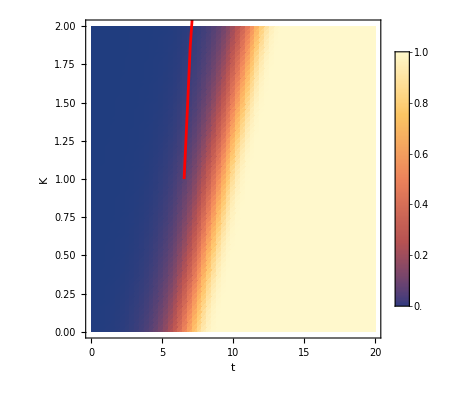

```mathematica
R0=0.5;
tmin=0;tmax=20;
Kmin=10^0;Kmax=10^2;

Show[
DensityPlot[R[t,K],{t,tmin,tmax},{K,Kmin,Kmax},
ScalingFunctions->{None,"Log10"},
PlotLegends->BarLegend[Automatic,LabelStyle->12],
FrameLabel->{"t","K"},
PlotPoints->60,MaxRecursion->2
],
ContourPlot[R[t,K]==R0,{t,tmin,tmax},{K,Kmin,Kmax},
ContourStyle->{Thick,Red}
]
]
```